# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineages other, Delta, Omicron BA.1, Omicron BA.2, Omicron BA.4 and Omicron BA.5.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-south-africa-ba4-ba5

```mathematica
dataset="omicron-south-africa-ba4-ba5";
```

```mathematica
imageSize=280;
```

```mathematica
gridCount=2;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron BA.1","Omicron BA.2","Omicron BA.4","Omicron BA.5"};
```

```mathematica
n=Length[variants]
```

6

### Colors

```mathematica
start[n_]:=0.1;
```

```mathematica
stop[n_]:=0.98;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Prepend[makeColors[n-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.31246632, 0.59399708, 0.72838912],RGBColor[0.5737267600000001, 0.73875072, 0.38814183999999996],RGBColor[0.86951232, 0.6566998, 0.23336048],RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001]}

```mathematica
legendPanel=PointLegend[colors[[2;;n]],variants[[2;;n]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Locations

```mathematica
locationsToDrop={"Mpumalanga","Western Cape Province"};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2022-01-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-04-10

```mathematica
countries=Union[seqData[[All,2]]]
```

{Gauteng,KwaZulu-Natal,Mpumalanga,Western Cape Province}

```mathematica
countries=Complement[countries,locationsToDrop]
```

{Gauteng,KwaZulu-Natal}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-10;;-1]]&,countries]
```

{Gauteng→{{2022-04-01,20},{2022-04-02,1},{2022-04-03,0},{2022-04-04,4},{2022-04-05,7},{2022-04-06,11},{2022-04-07,5},{2022-04-08,0},{2022-04-09,0},{2022-04-10,0}},KwaZulu-Natal→{{2022-04-01,15},{2022-04-02,4},{2022-04-03,1},{2022-04-04,0},{2022-04-05,0},{2022-04-06,2},{2022-04-07,10},{2022-04-08,12},{2022-04-09,2},{2022-04-10,1}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=30;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_,index_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[index]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_,index_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[index]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountriesBA4=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron BA.4"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
modeledFreqsForCountriesBA5=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron BA.5"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountriesBA4=Map[constructGrowthRateLegend[modeledGrowthRate[#[[5]]],variants[[5]],legendStartingPointY- 0.09,colors[[5]]]&,freqsForCountries];
```

```mathematica
legendsForCountriesBA5=Map[constructGrowthRateLegend[modeledGrowthRate[#[[6]]],variants[[6]],legendStartingPointY- 0.09,colors[[6]]]&,freqsForCountries];
```

```mathematica
panels=Table[logisticFreqPlotMultipleLineages[freqsForCountries[[i]],modeledFreqsForCountriesBA4[[i]],legendsForCountriesBA4[[i]],countries[[i]],5],{i,2}];
```

```mathematica
figLogisticBA4=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

| 
-Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis-ba4.png",figLogisticBA4,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_logistic-growth-transformed-axis-ba4.png

```mathematica
panels=Table[logisticFreqPlotMultipleLineages[freqsForCountries[[i]],modeledFreqsForCountriesBA5[[i]],legendsForCountriesBA5[[i]],countries[[i]],6],{i,2}];
```

```mathematica
figLogisticBA5=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

| 
-Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis-ba5.png",figLogisticBA4,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_logistic-growth-transformed-axis-ba5.png

BA.4 in Guateng

```mathematica
Map[retransformPrevSeries,freqsForCountries,{2}][[1,5,-5;;-1]]
```

{{2022-04-03,0.698412},{2022-04-04,0.749998},{2022-04-05,0.785711},{2022-04-06,0.777775},{2022-04-07,0.777775}}

BA.5 in Guateng

```mathematica
Map[retransformPrevSeries,freqsForCountries,{2}][[1,6,-5;;-1]]
```

{{2022-04-03,0.079365},{2022-04-04,0.0833332},{2022-04-05,0.107142},{2022-04-06,0.111111},{2022-04-07,0.111111}}

BA.4 in KwaZulu-Natal

```mathematica
Map[retransformPrevSeries,freqsForCountries,{2}][[2,5,-5;;-1]]
```

{{2022-04-03,0.0370369},{2022-04-04,0.0937497},{2022-04-05,0.103448},{2022-04-06,0.0740738},{2022-04-07,0.111111}}

BA.5 in KwaZulu-Natal

```mathematica
Map[retransformPrevSeries,freqsForCountries,{2}][[2,6,-5;;-1]]
```

{{2022-04-03,0.555553},{2022-04-04,0.624998},{2022-04-05,0.620688},{2022-04-06,0.555553},{2022-04-07,0.555553}}

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

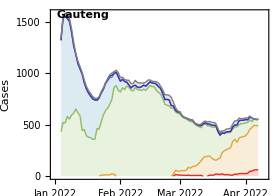
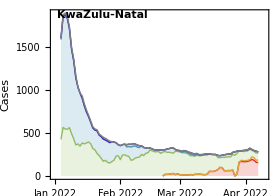
| 
-Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=1500;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,20,50,100,200,500,1000,2000,5000,10000,20000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,20,50,100,200,500,1000,2000,5000,10000,20000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_,variant_,index_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,variant];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[index]],FrameTicks->{{{10,20,50,100,200,500,1000,2000,5000,10000,20000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
panelA=Show[splitCaseLogPlot["Gauteng",constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather["Gauteng","Omicron BA.4"]],"Omicron BA.4",legendStartingPointY- 0.09,colors[[5]]]],splitCaseLogPlotModeledOmicron["Gauteng","Omicron BA.4",5]];
```

```mathematica
panelB=Show[splitCaseLogPlot["KwaZulu-Natal",constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather["KwaZulu-Natal","Omicron BA.5"]],"Omicron BA.5",legendStartingPointY- 0.09,colors[[6]]]],splitCaseLogPlotModeledOmicron["KwaZulu-Natal","Omicron BA.5",6]];
```

```mathematica
panels={panelA,panelB};
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

| 
-Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-south-africa-ba4-ba5_partitioned-log-cases.png